# Indivaria

Sompob Saralamba, Richard Maude, Wirichada Pan-Ngum, and Lisa White

Mahidol-Oxford Tropical Medicine Research Unit (MORU), Mahidol University, Thailand

## Introduction

With the present knowledge of malaria, the number of parasites in a patient before and during treatment can be estimated by using mathematical models. Mathematical models are used in studying in many aspects of malaria parasites for improving treatment. These models are different in their purposes and assumptions. They have been published in many scientific journals. A collection of these models there could be useful and helpful for the people who studies in the field of intrahost modelling of malaria parasites. At Mahidol-Oxford Tropical Medicine Research Unit (MORU), a computer software package called “Indivaria” has been developed. It is a Mathematica package which collected some published mathematical models for the dynamics of malaria paraistes in an infected patient without treatment and during treatment with antimalaria drugs.

## Using Indivaria

The main function or command of the package is IDVL. The IDVL function requires user to enter only a filename of an input file. This input file contains a list of the parameters and their values of a chosen model. The input file can be created by using any text editor such as Notedpad or Vim. In each input file the parameters of model ID (“model”) and its output form (“outform”) must be specified. The parameters of each model are different and can be shown by using the function ListPar.

IDVL is the main function of the package. The user has to enter the list of the parameters and their values of the model they choose in an input file. The parameters of each model are different and can be shown by using the fucntion ListPar.

IDVL["inputfile"] | performs the calculation of the model following the parameters in the input file.
ListPar[modelID,outform] | shows the list of parameters required by the model.

-Graphics-

Figure 1. The example of the input file.

To use Indivaria, the user has to load its packag first by using the function Get or Needs. Below is an example of using IDVL function to compare the observed and the modelled parasite count data from the patient during treatment with artesunate using the model proposed by Saralamba S, et al., PNAS (2011).

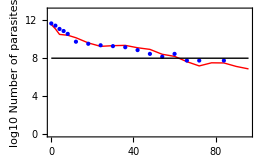
<< Indivaria`

IDVL["mod1_1.in"]
"******INDIVARIA*****"
"model"": "1.1
"outform"": "1
"********************"
"model"": "1.1
"parafile"": ""paraP002.csv"
"concfile"": ""P002.csv"
"initn"": ""6.02*10^11"
"pmr"": "12
"mu"": "13
"sigma"": "8
"lifecycle"": "48
"killzone"": ""{{6,20},{21,38},{39,44}}"
"everyh"": "24
"ndrug"": "7
"gamma"": ""{8.31521,3.96412,3.96412}"
"ec50"": ""{38.2193,0.662235,0.662235}"
"emin"": ""{0.0,0.0,0.0}"
"emax"": ""{99.9779,99.99,99.99}"
"1/alpha"": "7.78339
"outform"": "1
"runmax: "96
-Graphics-

The example of using IDVL function

#### List of the models

Model 1.0  The model proposed by Saralamba S., et al., 2011 PNAS.

******INDIVARIA*****

model: 1.1

outform: 1

********************

model: 1.1

parafile: paraP002.csv

concfile: P002.csv

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

killzone: {{6,20},{21,38},{39,44}}

everyh: 24

ndrug: 7

gamma: {8.31521,3.96412,3.96412}

ec50: {38.2193,0.662235,0.662235}

emin: {0.0,0.0,0.0}

emax: {99.9779,99.99,99.99}

1/alpha: 7.78339

outform: 1

runmax: 96

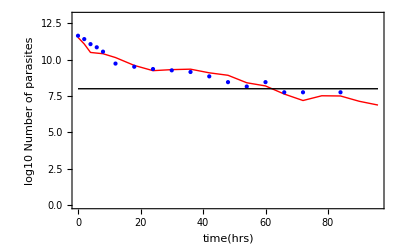

```mathematica
IDVL["mod1_1.in"]
```

```mathematica
IDVL["model1_2.in"]
```

******INDIVARIA*****

model: 1.2

outform: 0

********************

model: 1.2

parafile: paraP002.csv

concfile: P002.csv

runsteps: 50

outname: testP002

outform: 0

testP002.csv exists already.

$Aborted

```mathematica
IDVL["mod1_3.in"]
```

******INDIVARIA*****

model: 1.3

outform: 2

********************

model: 1.3

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

concfile: P002.csv

everyh: 24

ndrug: 7

ec50: 38.2193

runsteps: 70

dorfrac: 0.05

dortime: 7

outform: 2

{{0,11.7435},{1,11.7114},{2,10.9346},{3,10.5927},{4,10.3803},{5,10.2524},{6,10.1866},{7,10.1555},{8,10.143},{9,10.1435},{10,10.1564},{11,10.6263},{12,10.6179},{13,10.6104},{14,10.6008},{15,10.5869},{16,10.5675},{17,10.542},{18,10.51},{19,10.4715},{20,10.428},{21,10.3782},{22,10.3201},{23,10.2512},{24,10.168},{25,10.134},{26,9.33964},{27,9.28193},{28,9.36863},{29,9.47583},{30,9.58513},{31,9.69015},{32,9.7885},{33,9.87969},{34,9.96393},{35,10.0416},{36,10.103},{37,10.1439},{38,10.1652},{39,10.1706},{40,10.1644},{41,10.1506},{42,10.1319},{43,10.1103},{44,10.0884},{45,10.0664},{46,10.0441},{47,10.0214},{48,9.99767},{49,9.97194},{50,8.7583},{51,8.06267},{52,7.75695},{53,7.63762},{54,7.59201},{55,7.57322},{56,7.56376},{57,7.55851},{58,7.55727},{59,7.55399},{60,7.55381},{61,7.54953},{62,7.53781},{63,7.51985},{64,7.49842},{65,7.47473},{66,7.44802},{67,7.42258},{68,7.39648},{69,7.36755},{70,7.33234}}

```mathematica
IDVL["mod1_4.in"]
```

******INDIVARIA*****

model: 1.4

outform: 1

********************

model: 1.4

initn: 6.02*10^11

lifecycle: 48

mu: 13

sigma: 8

pmr: 12

endring: 26

runsteps: 70

outform: 1

{5.72801×10^11,5.64308×10^11,5.53997×10^11,5.41678×10^11,5.27201×10^11,5.10469×10^11,4.91458×10^11,4.70239×10^11,4.46996×10^11,4.22041×10^11,3.95835×10^11,3.69×10^11,3.42332×10^11,3.16818×10^11,2.93643×10^11,2.74199×10^11,2.60099×10^11,2.53175×10^11,2.55479×10^11,2.69272×10^11,2.97×10^11,3.41252×10^11,4.04693×10^11,4.89983×10^11,5.99661×10^11,7.36013×10^11,9.00923×10^11,1.10421×10^12,1.33636×10^12,1.59734×10^12,1.88618×10^12,2.20087×10^12,2.53837×10^12,2.89466×10^12,3.26486×10^12,3.64341×10^12,4.02429×10^12,4.40123×10^12,4.76802×10^12,5.1187×10^12,5.44782×10^12,5.7505×10^12,6.02265×10^12,6.2609×10^12,6.46264×10^12,6.62592×10^12,6.74937×10^12,6.83212×10^12,6.87361×10^12,6.7717×10^12,6.64796×10^12,6.50014×10^12,6.32642×10^12,6.12562×10^12,5.89749×10^12,5.64287×10^12,5.36395×10^12,5.06449×10^12,4.75002×10^12,4.42799×10^12,4.10799×10^12,3.80182×10^12,3.52371×10^12,3.29039×10^12,3.12119×10^12,3.0381×10^12,3.06574×10^12,3.23126×10^12,3.564×10^12,4.09502×10^12,4.85632×10^12}

```mathematica
lsout=IDVL["mod1_5.in"];
```

******INDIVARIA*****

model: 1.5

outform: 0

********************

model: 1.5

lambda: 1.

mu: 0.00833

beta: 0.1

alpha: 0.2

r: 16.

d: 72

initx: 10000

inity: 1.

inits: 0.

runsteps: 600

stepsize: 0.1

outform: 0

```mathematica
lsout[[1;;4]]
```

{{0.,10000.,1.,-3.88775×10^-23},{0.1,9991.43,1.31648,0.00392272},{0.2,9982.76,1.73788,0.00518257},{0.3,9973.95,2.29413,0.006847}}

```mathematica
lsout=IDVL["mod1_6.in"];
```

******INDIVARIA*****

model: 1.6

outform: 0

********************

model: 1.6

initx: {1,1,1,1}

r: 16

h: 0.05

initd: {1,1,1,1}

inits: {0.00001,0.00002,0.0001,0.001}

runsteps: 50

outform: 0

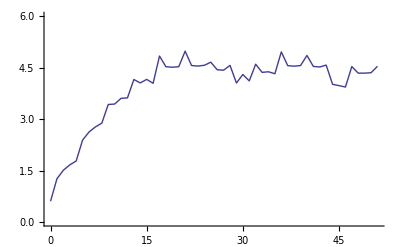

```mathematica
ls=Table[{lsout[[i,1]],Log10@lsout[[i,3]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6}]
```

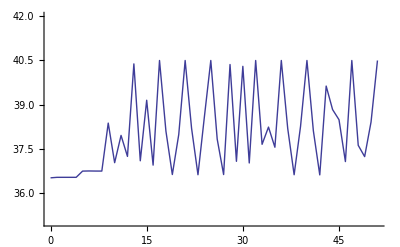

```mathematica
ls=Table[{lsout[[i,1]],lsout[[i,4]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{35,42}]
```

```mathematica
lsout=IDVL["mod1_7.in"];
```

******INDIVARIA*****

model: 1.7

outform: 0

********************

model: 1.7

initn: {1000,200}

lambdals: {0.0309,0.0438}

muls: {0.1,0.25}

r: 8.3

runsteps: 60

stepsize: 0.1

outform: 0

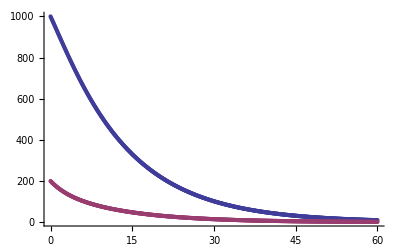

```mathematica
ListPlot[{lsout[[All,{1,2}]],lsout[[All,{1,3}]]},PlotRange->All]
```

```mathematica
ListPar[1.5,0]
```

{model,lambda,mu,beta,alpha,r,d,initx,inity,inits,runsteps,stepsize,outform}

## Indivaria Installation Instructions